```mathematica
Impedance[α0_,χ0_,U0_,θ0_,η0_,P0_]:=
Module[{α=α0,U=U0,P,rule,X,n,smoothingFunc,v,u,ϵ,g,system,R,RP,Dissipation},
(*α - dissipation, α=ν/ω, ω->ω(1+ⅈα);
χ - dimensionless wave vector magnitude; χ=Subscript[k, 0] L, and L=1;
U - anizatropy: p^2=4πe^2*n/m, b=eB/(mc), v=p^2/ω^2, u=b^2/ω^2, and with dissipation: v->v(1-ⅈα), u->U(1-ⅈα);
θ - angel between wave vector and XOZ;
η - angle between wave vector projection and density gradient direction;
P - wave polarisation in native mode (O-X); 2d-vector*)

(*=====================================================================================================================*)
u=U(1-ⅈ*α);
rule={$χ->χ0,$θ->θ0,$η->η0,$u->u,$X->X,$ϵ->ϵ,Subscript[$ϵ, l]->Subscript[ϵ, l],$g->g};
P=If[η0==0,Subscript[Υ, vp^s],Subscript[Υ, vp^r]].P0/.rule;(*vacuum polarisation*)
X=3;(*plasma boundary*)
n=0.1;(*smoothing width, in parts of plasma whight*)
smoothingFunc=Function[x,(1+(x/X)^(2/n))^-1]; v=Function[x,((X^2-x^2)/(X^2-1))*smoothingFunc[x]*(1-ⅈ*α)];
ϵ=Function[x,1-v[x]/(1-u)];Subscript[ϵ, l]=Function[x,1-v[x]];g=Function[x,(√u)/(1-u)v[x]];
(*=====================================================================================================================*)
system={eq,ic}/.rule;
Subscript[R, vacuum]=(Subscript[$R, general]/.NDSolve[system,{tt[x],st[x],ts[x],ss[x]},{x,-2X,2X}])⟦1⟧;
RP=Subscript[R, vacuum].P/.x->-2X;
Dissipation=1-(Abs[RP⟦1⟧]^2+Abs[RP⟦2⟧]^2)/(Abs[P⟦1⟧]^2+Abs[P⟦2⟧]^2);
{Dissipation,Subscript[R, vacuum],X}
];
```

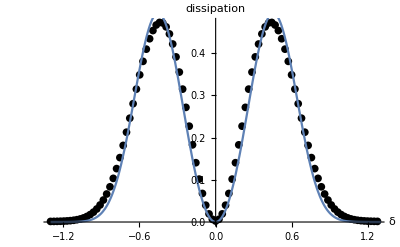

```mathematica
δDissipation={};
χ=30;α=0;η=0;
δbegining=-1.3;δend=1.3;δnstep=100;
ProgressIndicator[Dynamic[(δ-δbegining)/(δend-δbegining)]]
For[δ=δbegining,δ<δend,δ+=(δend-δbegining)/δnstep,
δDissipation=Append[δDissipation,{δ,Impedance[10^-5,χ,(α*χ^(-2/3))^2,ArcSin[δ*χ^(-1/3)],η,{0,1}]⟦1⟧}];
];
Clear[χ,α,δ,η];

experiment=ListPlot[δDissipation,PlotRange->Full,AxesLabel->{δ,dissipation},PlotStyle->Black];
fittingFunction=Function[δ,a*δ^2 *Exp[-b*Abs[δ]^3 ]];
fit=FindFit[δDissipation,fittingFunction[δ],{a,b},δ];
theory=Plot[fittingFunction[δ]/.fit,{δ,δbegining,δend},PlotRange->Full,PlotLegends->ToString[fittingFunction[δ]/.fit,TraditionalForm]];

result=Show[{experiment,theory}]

(*SaveData["results/isotropism/isotropism.csv",δDissipation,"CSV"]
SaveData["results/isotropism/isotropism.pdf",result,"PDF"]*)
```

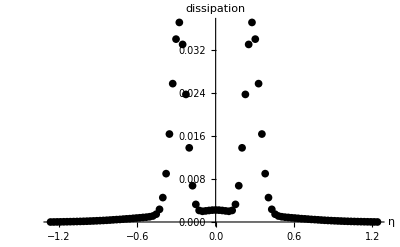

```mathematica
ηDissipation={};
χ=30;υ=0.01;θ=0;
ηbegining=-π/2+ArcSin[√((√υ)/(1+√υ))];ηend=π/2-ArcSin[√((√υ)/(1+√υ))];ηnstep=100;
ProgressIndicator[Dynamic[(η-ηbegining)/(ηend-ηbegining)]]
For[η=ηbegining,η<ηend,η+=(ηend-ηbegining)/ηnstep,
ηDissipation=Append[ηDissipation,{η,Impedance[10^-5,χ,υ,θ,η,{1,0}]⟦1⟧}];
];
Clear[χ,υ,θ,η];

experiment=ListPlot[ηDissipation,PlotRange->Full,AxesLabel->{η,dissipation},PlotStyle->Black];
(*fittingFunction=Function[δ,a*δ^2 *Exp[-b*Abs[δ]^3 ]];
fit=FindFit[δDissipation,fittingFunction[δ],{a,b},δ];
theory=Plot[fittingFunction[δ]/.fit,{δ,δbegining,δend},PlotRange->Full,PlotLegends->ToString[fittingFunction[δ]/.fit,TraditionalForm]];*)

result=Show[{experiment(*,theory*)}]

(*SaveData["results/isotropism/isotropism.csv",βDissipation,"CSV"]
SaveData["results/isotropism/isotropism.pdf",result,"PDF"]*)
```

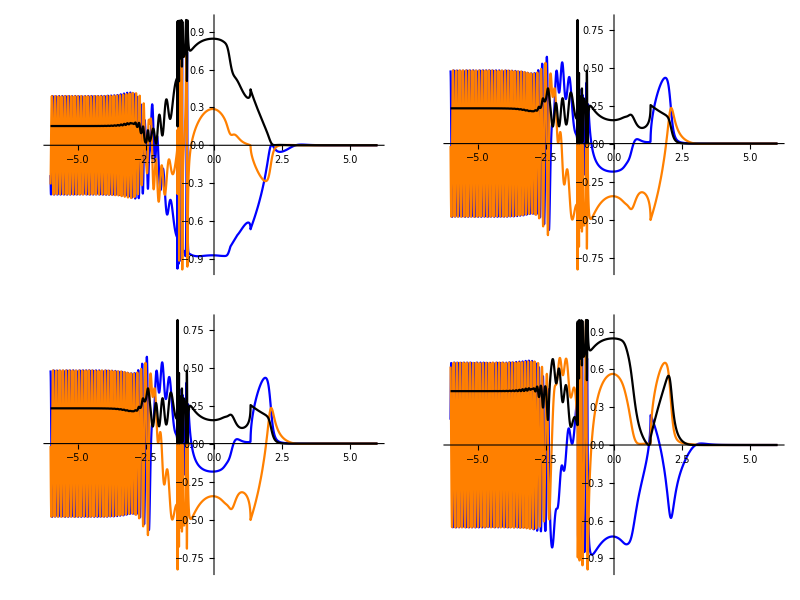
{0.886336,(-Graphics-)}

```mathematica
χ=30;υ=0.1;η=0.5;θ=0;(*ArcSin[√((√υ)/(1+√υ))]*)
Impedance[10^-5,χ,υ,θ,η,{0,1}];
{%⟦1⟧,Table[Plot[{Re[%⟦2⟧⟦i,j⟧],Im[%⟦2⟧⟦i,j⟧],Abs[%⟦2⟧⟦i,j⟧]^2},{x,-2%⟦3⟧,2%⟦3⟧},ImageSize->Medium,PlotRange->Full,PlotStyle->{Blue,Orange,Black}],{i,1,2},{j,1,2}]//MatrixForm}
Clear[χ,υ,θ,η]
```